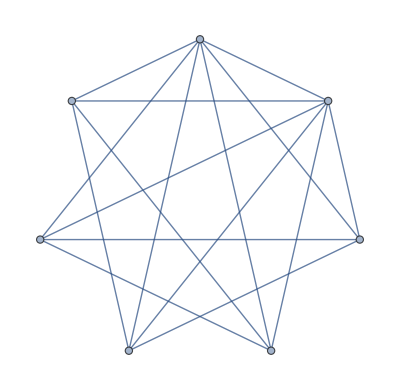

```mathematica
gr=EdgeDelete[CompleteGraph[7],EdgeList[CycleGraph[5]]]
```

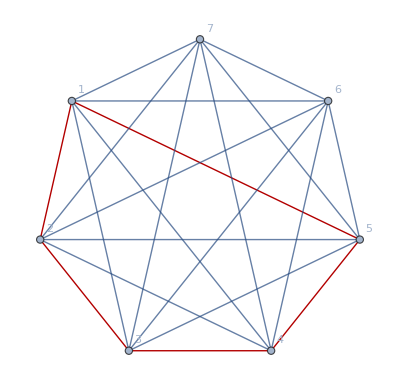
{-Graphics-,0,False}

```mathematica
With[{h=gr},{Graph[CompleteGraph[VertexCount[h]],GraphHighlight->EdgeList[GraphComplement[h]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],ChromaticPolynomial[h,4],MaximalPlanarQ[h]}]
```

```mathematica
MaximalPlanarQ[gr]
```

False

```mathematica
PlanarGraphQ[gr]
```

False

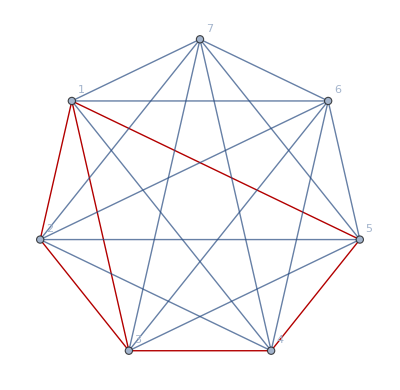
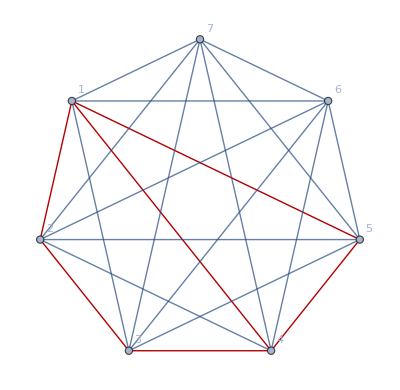
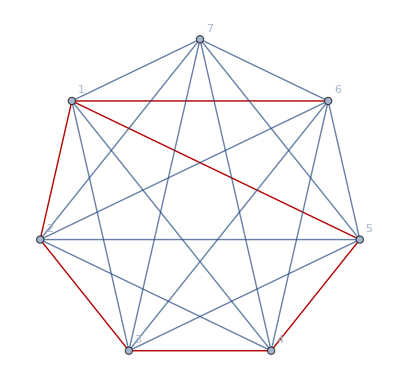
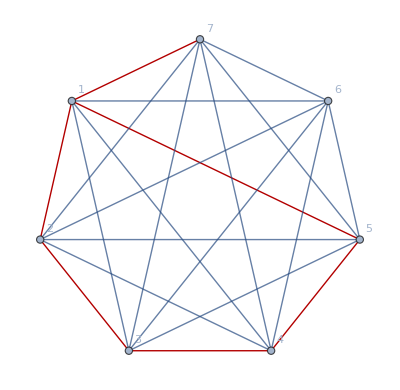
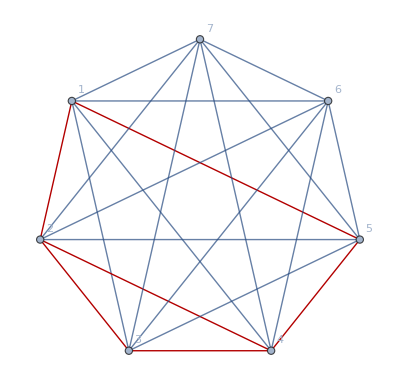
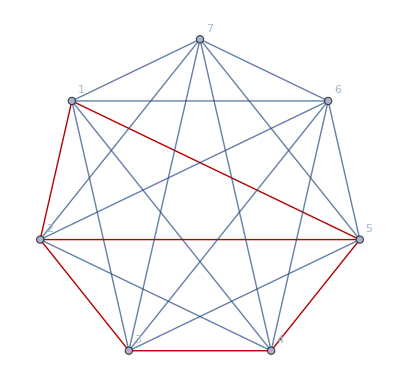
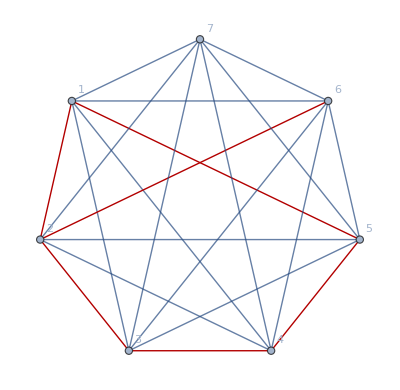
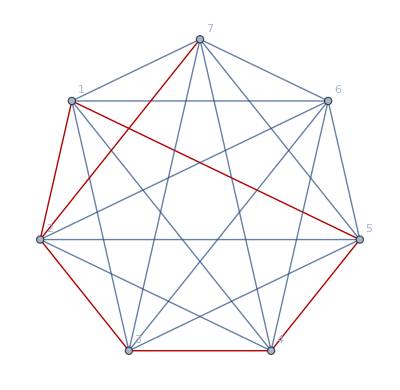
{{-Graphics-,1,True},{-Graphics-,1,True},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,True},{-Graphics-,1,True},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,True},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,1,False},{-Graphics-,5,True}}

```mathematica
Table[With[{h=EdgeDelete[gr,e]},{Graph[CompleteGraph[VertexCount[h]],GraphHighlight->EdgeList[GraphComplement[h]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],ChromaticPolynomial[h,4]/24,MaximalPlanarQ[h]}],{e,EdgeList[gr]}]
```